## OBC strained graphene

```mathematica
<<MaTeX`
a=0.142; dunit="\\ [{\\rm nm}]";
(*a=1.0;dunit="/d_0";*)
inFrac=0.3; (* fraction of in-scattering region *)
nuc=11; (* number of unit cells in the final region*)
width=3*nuc a; (* upscaled width and heigth to match nuc×nuc *)
height=width;

(*nuc=11;
width=3 nuc a;
height=1.1*width;*)

L=Max[{width,height}];
L1=(L+a)/a;
L2=(L+a)/a;
(* primitive lattice vectors *)
a1=a/2{3,√3,0};
a2=a/2{3,-√3,0};
b1={a,0,0};
uc ={0*b1,b1};

ss = 0.3a;ts=0.1a;
latt=Flatten[Table[{n1*a1+n2*a2+uc[[i]],i},{n1,L1},{n2,L2},{i,Length[uc]}],2];
meanPosition=Mean[latt[[All,1]]];
latt[[All,1]]=(#-meanPosition)&/@latt[[All,1]];
lattRegion=DeleteCases[latt,_?(Not[(-width/2<#[[1,1]]<width/2)&&(-height/2<#[[1,2]]<(height)/2)]&)];

rB=Max[lattRegion[[All,1]][[All,1]]];lB=Min[lattRegion[[All,1]][[All,1]]];
tB=Max[lattRegion[[All,1]][[All,2]]];bB=Min[lattRegion[[All,1]][[All,2]]];
lrPos=Flatten[Position[lattRegion[[All,1]][[All,1]],n_ /; n==#]]&/@{rB,lB};
tbPos=Flatten[Position[lattRegion[[All,1]][[All,2]],n_ /; n==#]]&/@{tB,bB};
bPos=Join[lrPos,tbPos];

cL=IntegerPart[Length[tbPos[[2]]]/2];
inR = IntegerPart[cL*inFrac];
inPos = tbPos[[2,cL-inR+1;;-(cL-inR+1)]];
bPos=Complement[#,inPos]&/@bPos;

lattCols={Darker[Gray],Lighter[Gray]};
boundaryCols={Darker[Green],Lighter[Green]};
injectionCols={Darker[Blue],Lighter[Blue]};

latt=Chop[lattRegion];
latt[[All,1]]=(#[[1]]-{Min[latt[[All,1,1]]],Min[latt[[All,1,2]]],Min[latt[[All,1,3]]]})&/@latt;
lattBR=latt[[#]]&/@Flatten[bPos];
lattIN=latt[[#]]&/@Flatten[inPos];
dimH = Length[latt];
Clear[lattRegions]
Evaluate[Table[lattRegions[i],{i,Length[uc]}]]=Evaluate[Table[DeleteCases[latt,_?(Not[#[[2]]==i]&)],{i,Length[uc]}]];
lattPlot=Graphics3D[Table[{lattCols[[#[[2]]]],Sphere[#[[1]],ss]}&/@lattRegions[i],{i,{1,2}}]];
boundaryPlot=Graphics3D[{boundaryCols[[#[[2]]]],Sphere[#[[1]],ss]}&/@lattBR];
injectionPlot=Graphics3D[{injectionCols[[#[[2]]]],Sphere[#[[1]],ss]}&/@lattIN];
nodesPlot=Show[lattPlot,boundaryPlot,injectionPlot,ViewPoint->Top,Axes->True,AxesLabel->MaTeX[#<>dunit&/@{"x","y","z"}]]

dist[n1_,n2_]:=Norm[n2-n1];
dists=Outer[dist,latt[[All,1]],latt[[All,1]],1];
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
(*neighbors={#,#}&/@latt[[All,1]];*)
neighbors=Position[dists,x_/;Abs[x-#]<1*^-8,3]&/@ddists[[{2}]];//AbsoluteTiming
nnPlot=Graphics3D[{{Black,CapForm["Butt"],Tube[{latt[[#[[1]],1]],latt[[#[[2]],1]]},ts]}&/@neighbors[[1]]},ViewPoint->Top];
Show[nodesPlot,nnPlot,ViewPoint->Top,Axes->True,AxesLabel->MaTeX[#<>dunit&/@{"x","y","z"}]]
```

-Graphics3D-

{0.401238,Null}

-Graphics3D-

```mathematica
<<MaTeX`
a=0.142; dunit="\\ [{\\rm nm}]";
(*a=1.0;dunit="/d_0";*)
inFrac=0.3; (* fraction of in-scattering region *)
nuc=20; (* number of unit cells in the final region*)
width=3*nuc a; (* upscaled width and heigth to match nuc×nuc *)
height=width;

(*nuc=11;
width=3 nuc a;
height=1.1*width;*)

L=Max[{width,height}];
L1=(L+a)/a;
L2=(L+a)/a;
(* primitive lattice vectors *)
a1=a/2{3.,√3,0};
a2=a/2{3.,-√3,0};
b1={a,0,0};
uc ={0*b1,b1};

ss = 0.3a;ts=0.1a;
latt=Flatten[Table[{n1*a1+n2*a2+uc[[i]],i},{n1,L1},{n2,L2},{i,Length[uc]}],2];
nns=Keys[ArrayRules[AdjacencyMatrix[NearestNeighborGraph[latt[[All,1]]]]]][[;;-2]];
Graphics3D[{Point[latt[[All,1]]],Line[latt[[#,1]]]&/@nns},ViewPoint->Top]
```

-Graphics3D-

```mathematica
nnodes=(latt//Length)
Length[nns]/nnodes//N
```

7442

2.96721

```mathematica
(* gaussian strain profile *)
Clear[strainFieldGaussian]
strainFieldGaussian[n_,σn_]:=N[1/(√(2π σn^2)) Exp[-Norm[n]^2/(2 σn^2) ]]
nhat={0,0,2L a};r0=Mean[latt[[All,1]]]+{L/4,L/4,0};σd=L/6;
deformedLatt={Chop[#[[1]]+strainFieldGaussian[#[[1]]-r0,σd]*nhat],#[[2]]}&/@latt;
deformedLattBR=deformedLatt[[#]]&/@Flatten[bPos];
deformedLattIN=deformedLatt[[#]]&/@Flatten[inPos];
Clear[deformedLattRegions]
Evaluate[Table[deformedLattRegions[i],{i,Length[uc]}]]=Evaluate[Table[DeleteCases[deformedLatt,_?(Not[#[[2]]==i]&)],{i,Length[uc]}]];
deformedLattPlot=Graphics3D[Table[{lattCols[[#[[2]]]],Sphere[#[[1]],ss]}&/@deformedLattRegions[i],{i,{1,2}}]];
deformedBoundaryPlot=Graphics3D[{boundaryCols[[#[[2]]]],Sphere[#[[1]],ss]}&/@deformedLattBR];
deformedInjectionPlot=Graphics3D[{injectionCols[[#[[2]]]],Sphere[#[[1]],ss]}&/@deformedLattIN];
deformedNodesPlot=Show[deformedLattPlot,deformedBoundaryPlot,deformedInjectionPlot];
maxZ=Max[deformedLatt[[All,1,3]]];
Clear[cs]
(*cs[x_]:=ColorData["PigeonTones"][x];*)
(*cs[x_]:=Directive[Black,Opacity[1-x]];*)
cs[x_]:=Directive[Blend[{Black,White},x]];
deformedNNPlot=Graphics3D[{{Black,CapForm["Butt"],Tube[{deformedLatt[[#[[1]],1]],deformedLatt[[#[[2]],1]]},ts]}&/@neighbors[[2]]},ViewPoint->Top,AxesLabel->MaTeX[#<>dunit&/@{"x","y","z"}]];
Show[deformedNodesPlot,deformedNNPlot,ViewPoint->{Right,Above},Axes->True,AxesLabel->MaTeX[#<>dunit&/@{"x","y","z"}]]
Show[%,ViewPoint->{Front},Axes->True,AxesLabel->MaTeX[#<>dunit&/@{"x","y","z"}]]
```

-Graphics3D-

-Graphics3D-

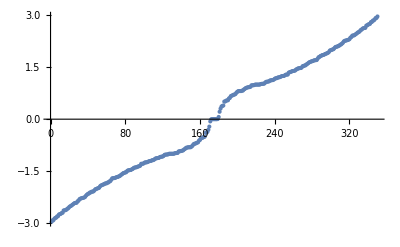

True

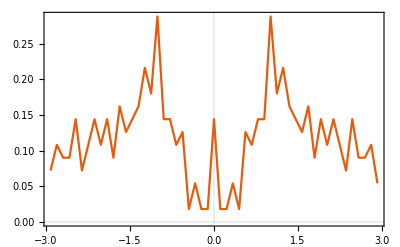

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];

(* now the Hamiltonian matrix is simply given by the nearest neighbor connections *)
t0=1.0;
H=Normal[SparseArray[#-> t0&/@neighbors[[2]]]];
{energies,wavefunctions}=orderedEigensystem[H]//Sort;
imEnergies=Im[energies];
energies=Re[energies];
ListPlot[energies]
max=Max[energies];
min=Min[energies];
DeleteDuplicates[Chop[wavefunctions†.H.wavefunctions-DiagonalMatrix[energies]]//Flatten]=={0}
(*Histogram[energies,{min,max,(max-min)/54},"Probability",PlotRange->{{-1.5,1.5},Automatic}]*)
{bene,bvals}=HistogramList[energies,{min,max,(max-min)/53},Probability];
<<MaTeX`
ListPlot[{MovingAverage[bene,2],bvals*2*π}ᵀ,Joined->True,PlotTheme->"Scientific",FrameLabel->MaTeX[{"E/t0","D(E)"}]]
```

### The Knitting algorithm

```mathematica
Graphics3D[{Point[#[[1]]]&/@deformedLatt,Line[deformedLatt[[#,1]]&/@neighbors[[2]]]}]
```

-Graphics3D-

```mathematica
.
```

### NEGF

```mathematica
(* now the Hamiltonian matrix is simply given by the nearest neighbor connections *)
Clear[t0,β,d]
t0=1.0;β=3.37;vF=3t0 a/2;
d[n1_,n2_,latt_]:=(Norm[latt[[n1,1]]-latt[[n2,1]]]-a)/a
Hdef=Normal[SparseArray[#-> t0*Exp[-β d[#[[1]],#[[2]],deformedLatt]]&/@neighbors[[2]]]];
{energies,wavefunctions}=orderedEigensystem[Hdef]//Sort;
imEnergies=Im[energies];
energies=Re[energies];
ListPlot[energies]
max=Max[energies];
min=Min[energies];
DeleteDuplicates[Chop[wavefunctions†.Hdef.wavefunctions-DiagonalMatrix[energies]]//Flatten]=={0}
(*Histogram[energies,{min,max,(max-min)/54},"Probability",PlotRange->{{-1.5,1.5},Automatic}]*)
{bene,bvals}=HistogramList[energies,{min,max,(max-min)/53},Probability];
<<MaTeX`
ListPlot[{MovingAverage[bene,2],bvals*2*π}ᵀ,Joined->True,PlotTheme->"Scientific",FrameLabel->MaTeX[{"E/t0","D(E)"}]]
```

```mathematica
MinMax[t0*Exp[-β d[#[[1]],#[[2]],latt]]&/@neighbors[[2]]]
MinMax[t0*Exp[-β d[#[[1]],#[[2]],deformedLatt]]&/@neighbors[[2]]]
MinMax[t0*Exp[-β d[#[[1]],#[[2]],deformedLatt]]&/@neighbors[[2]]]
```

```mathematica
Graphics3D[{{cs[1-Exp[-β d[#[[1]],#[[2]],deformedLatt]]],CapForm["Butt"],Tube[{deformedLatt[[#[[1]],1]],deformedLatt[[#[[2]],1]]},ts]}&/@neighbors[[2]]},ViewPoint->Above,Background->Black]
```

```mathematica
η=1/t0;
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)];

ene=1.1t0;
Kp={0,(+4π)/(3 √3),0};
Km={0,(-4π)/(3 √3),0};
Cp=0.;
Cm=1.;
kx=0;
ky=ene;
ϕ=Arg[ⅈ kx + ky];
σ=Sign[ene];

Clear[χ]
χ[1][r_,k_,σ_,ϕ_]:=Cm*ⅇ^(ⅈ(k+Km).r)+Cp*ⅇ^(ⅈ(k+Kp).r)
χ[2][r_,k_,σ_,ϕ_]:=σ Cm ⅇ^(ⅈ(k+Km).r + ⅈ ϕ)-σ Cp ⅇ^(ⅈ(k+Kp).r - ⅈ ϕ)
inTuples=Tuples[{inPos,inPos}];
ΣinP=0*H;
(ΣinP[[Sequence@@#]]=χ[deformedLatt[[#[[1]],2]]][deformedLatt[[#[[1]],1]],{kx,ky,0},+1,ϕ]* χ[deformedLatt[[#[[2]],2]]][deformedLatt[[#[[2]],1]],{kx,ky,0},+1,ϕ])&/@inTuples;
G=Inverse[N[ene*IdentityMatrix[Dimensions[H]]-H-Σ]];
GP = G.ΣinP.G†;
GP=GP/Max[Abs[Diagonal[GP,1]]];
nP = Re[Diagonal[(GP+GP†)]];
ppP = Abs[nP]/If[(w=Max[Abs[nP]])>1*^-8,w,1];

current=Graphics3D[{{Blend[{Red,White},1-(#[[1]])^(1/2)],Sphere[#[[2]],0ss]}&/@({ppP,latt[[All,1]]}ᵀ),{{Blend[{Red,White},1-Abs[Im[GP[[Sequence@@#]]]]],CapForm["Butt"],Tube[{latt[[All,1]][[#[[1]]]],latt[[All,1]][[#[[2]]]]},ts]}&/@neighbors[[2]]}}];
Show[nodesPlot,nnPlot,current,ViewPoint->{Right,Above},Boxed->False,Background->Black,Axes->False]
Show[nodesPlot,nnPlot,current,ViewPoint->Above,Boxed->False,Background->Black,Axes->False]
```

```mathematica
η=1/t0;
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)];

ene=1.2t0;
Kp={0,(+4π)/(3 √3),0};
Km={0,(-4π)/(3 √3),0};
Cp=0.;
Cm=1.;
kx=0;
ky=ene;
ϕ=Arg[ⅈ kx + ky];
σ=Sign[ene];

Clear[χ]
χ[1][r_,k_,σ_,ϕ_]:=Cm*ⅇ^(ⅈ(k+Km).r)+Cp*ⅇ^(ⅈ(k+Kp).r)
χ[2][r_,k_,σ_,ϕ_]:=σ Cm ⅇ^(ⅈ(k+Km).r + ⅈ ϕ)-σ Cp ⅇ^(ⅈ(k+Kp).r - ⅈ ϕ)
inTuples=Tuples[{inPos,inPos}];
ΣinP=0*H;
(ΣinP[[Sequence@@#]]=χ[deformedLatt[[#[[1]],2]]][deformedLatt[[#[[1]],1]],{kx,ky,0},+1,ϕ]* χ[deformedLatt[[#[[2]],2]]][deformedLatt[[#[[2]],1]],{kx,ky,0},+1,ϕ])&/@inTuples;
G=Inverse[N[ene*IdentityMatrix[Dimensions[Hdef]]-Hdef-Σ]];
GP = G.ΣinP.G†;
GP=GP/Max[Abs[Im[Diagonal[GP,1]]]];
nP = Re[Diagonal[(GP+GP†)]];
ppP = Abs[nP]/If[(w=Max[Abs[nP]])>1*^-8,w,1];

current=Graphics3D[{{Blend[{Red,White},1-(#[[1]])^(1/2)],Sphere[#[[2]],0ss]}&/@({ppP,deformedLatt[[All,1]]}ᵀ),{{Blend[{Red,White},1-Abs[Im[GP[[Sequence@@#]]]]],CapForm["Butt"],Tube[{deformedLatt[[All,1]][[#[[1]]]],deformedLatt[[All,1]][[#[[2]]]]},ts]}&/@neighbors[[2]]}}];
Show[deformedNodesPlot,deformedNNPlot,current,ViewPoint->Above,Boxed->False,Background->Black]
Show[deformedNodesPlot,deformedNNPlot,current,ViewPoint->{Right,Above},Boxed->False,Background->Black]
```